## RegularStar-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 15:52:42
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
p=RegularStar[7, 2]
```

{{2.,0.},{0.900969,0.433884},{1.24698,1.56366},{0.222521,0.974928},{-0.445042,1.94986},{-0.62349,0.781831},{-1.80194,0.867767},{-1.,1.22465×10^-16},{-1.80194,-0.867767},{-0.62349,-0.781831},{-0.445042,-1.94986},{0.222521,-0.974928},{1.24698,-1.56366},{0.900969,-0.433884}}

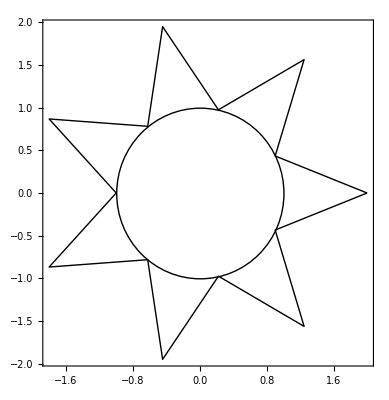

```mathematica
Show[Boundary[p],Graphics[Circle[{0,0}, 1]],  Frame-> True]
```

```mathematica
q=RegularStar[7, 2,0,  2.5, -1, Pi/3]
```

{{1.,-1.73205},{1.38987,-0.237907},{4.00892,0.874663},{2.22204,1.02595},{3.99904,2.82274},{1.38097,1.51725},{0.977803,2.64523},{-0.5,0.866025},{-2.77974,0.475815},{-2.00446,-0.437331},{-4.44408,-2.0519},{-1.99952,-1.41137},{-2.76194,-3.03449},{-0.488901,-1.32262}}

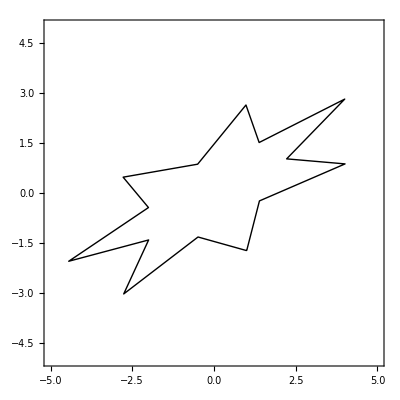

```mathematica
Show[Boundary[q], Frame-> True, PlotRange-> {{-5,5}, {-5,5}}, AspectRatio-> 1]
```

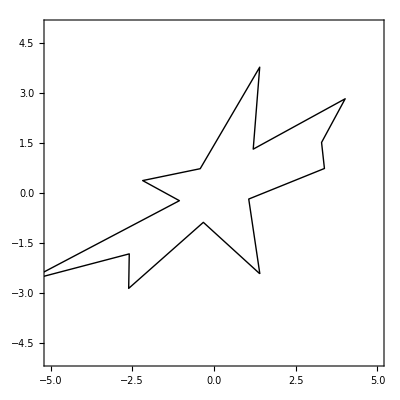

```mathematica
r=RegularStar[7, 2,0,  2.5, .5, Pi/3]; Show[Boundary[r], Frame-> True, PlotRange-> {{-5,5}, {-5,5}}, AspectRatio-> 1]
```